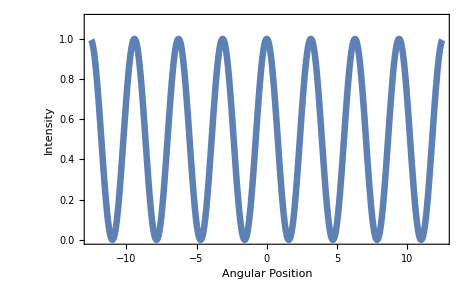

```mathematica
range=12.5;
p1=Plot[Cos[theta]^2,{theta,-range,range},PlotRange->{{-range,range},{0,1.1}},
Frame->True,FrameStyle->Black,
FrameLabel->{"Angular Position","Intensity","",""},
BaseStyle->FontSize->16,
ImageSize->6.5*72,
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],
PlotStyle->Thickness[0.01]
]
```

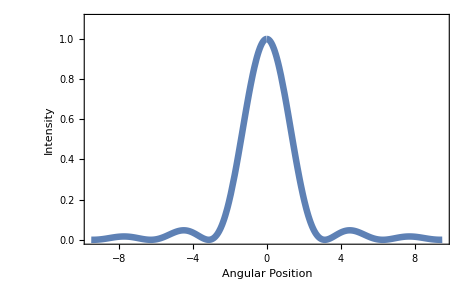

```mathematica
range=9.5;
p2=Plot[(Sin[theta]/theta)^2,{theta,-range,range},PlotRange->{{-range,range},{0,1.1}},
Frame->True,FrameStyle->Black,
FrameLabel->{"Angular Position","Intensity","",""},
BaseStyle->FontSize->16,
ImageSize->6.5*72,
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],
PlotStyle->Thickness[0.01]
]
```

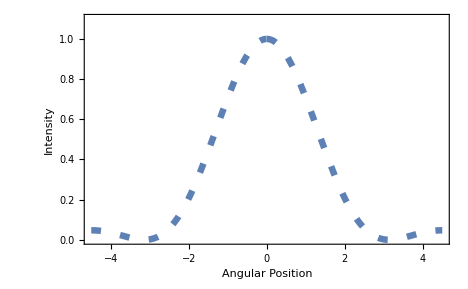

```mathematica
range=4.5;
p3=Plot[(Sin[theta]/theta)^2,{theta,-range,range},PlotRange->{{-range,range},{0,1.1}},
Frame->True,FrameStyle->Black,
FrameLabel->{"Angular Position","Intensity","",""},
BaseStyle->FontSize->16,
ImageSize->6.5*72,
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],
PlotStyle->{Thickness[0.01],Dashing[{0.015,0.03}]}
]
```

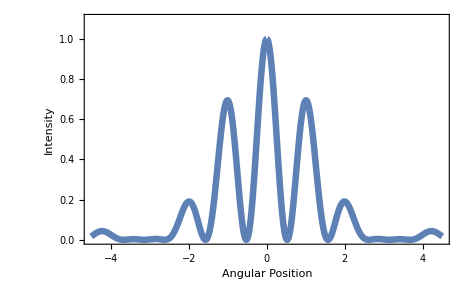

```mathematica
range=4.5;
p4=Plot[Cos[3*theta]^2*(Sin[theta]/theta)^2,{theta,-range,range},PlotRange->{{-range,range},{0,1.1}},
Frame->True,FrameStyle->Black,
FrameLabel->{"Angular Position","Intensity","",""},
BaseStyle->FontSize->16,
ImageSize->6.5*72,
FrameTicksStyle->Directive[FontOpacity->0,FontSize->0],
PlotStyle->Thickness[0.01]
]
```

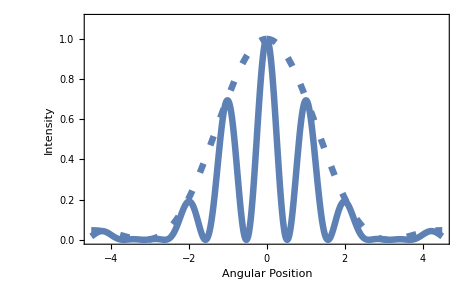

```mathematica
p5=Show[p3,p4]
```

```mathematica
Export["/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig1.pdf",p1]
Export["/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig2.pdf",p2]
Export["/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig3.pdf",p5]
```

/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig1.pdf

/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig2.pdf

/run/media/gilfoyle/KINGSTON/132s20/labs/myLabManual/diffractionOfLight/diffractionFig3.pdf